```mathematica
golaygreedybasis = {255,4080,15555,27030,65535,261289,457162,1048560,2027144,4193429,8317147,16777215};
golaygreedycode=IntegerDigits[#,2,24]&/@Sort[BitXor@@#&/@Subsets[golaygreedybasis]];
```

```mathematica
Length[golaygreedycode]
```

4096

```mathematica
golaygreedycode[[1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
leech1=Join[Permutations[{4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}],
Permutations[{-4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}],
Permutations[{-4,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]];
```

```mathematica
Length[leech1]
```

1104

```mathematica
2*Select[golaygreedycode,Total[#]==8&]
-2*Select[golaygreedycode,Total[#]==8&]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2},{0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,0,0,0,0,2,2,2,2},{0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,0,0,0,0},753,{2,2,2,2,0,0,0,0,0,0,0,0,2,2,2,2,0,0,0,0,0,0,0,0},{2,2,2,2,0,0,0,0,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0},{2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
 |  |  |  |

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,-2,-2,-2,-2,-2},{0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,-2,0,0,0,0,-2,-2,-2,-2},{0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,-2,-2,-2,-2,-2,0,0,0,0},754,{-2,-2,-2,-2,0,0,0,0,-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0},{-2,-2,-2,-2,-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
 |  |  |  |

```mathematica
even2s=Join[{{2,2,2,2,2,2,2,2}},Permutations[{-2,-2,2,2,2,2,2,2}],
Permutations[{-2,-2,-2,-2,2,2,2,2}],Permutations[{-2,-2,-2,-2,-2,-2,2,2}],{{-2,-2,-2,-2,-2,-2,-2,-2}}];
```

```mathematica
pairmap[list1_,list2_]:=Block[{i=1,j=1,blist={}},For[i=1,i<24,i++;Piecewise[{{blist=Append[blist,0], list1[[i]]==0}, {{j,blist}={j+1,Append[blist,list2[[j]]]}, list1[[i]]==1}}]];blist]
pairmap[{1,1,0,0,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,0,0,0,0},{1,2,3,4,5,6,7,8}]
```

{1,0,0,0,2,0,0,3,0,4,5,0,6,0,7,0,8,0,0,0,0,0,0}

```mathematica
2,4,8
```

```mathematica
Length[Select[golaygreedycode,Total[#]==8&]]
```

759

```mathematica
Length[even2s]
```

```mathematica
128*759
```

97152

```mathematica
leech2=Partition[Flatten[Monitor[Table[pairmap[Select[golaygreedycode,Total[#]==8&][[k]],even2s[[l]]],{l,1,128},{k,1,759}],{(l-1)*759+k}]],24];
```

```mathematica
Length[leech2]
```

93104

```mathematica
Clear[t3tmat]
```

```mathematica
Take[Reverse[Sort[{2,1,3}]],{1,2}]
```

{3,2}

```mathematica
d2ist[t3tmat_]:=Block[{tvec=Map[Take[t3tmat.#,{1,2}]&,Table[PadLeft[IntegerDigits[i,2],3],{i,0,7}]]},
Sum[Sum[EuclideanDistance[tvec[[i]],tvec[[j]]],{i,1,j}],{j,1,8}]]
d3ist[t3tmat_]:=Block[{tvec=Map[Take[t3tmat.#,{1,2}]&,Table[PadLeft[IntegerDigits[i,2],3],{i,0,7}]]},
Sum[Total[Take[Reverse[Sort[Table[EuclideanDistance[tvec[[i]],tvec[[j]]],{i,1,j}]]],{1,2}]],{j,2,8}]]
d4ist[t3tmat_]:=Block[{tvec=Map[Take[t3tmat.#,{1,2}]&,Table[PadLeft[IntegerDigits[i,2],4],{i,0,15}]]},
Sum[Sum[EuclideanDistance[tvec[[i]],tvec[[j]]],{i,1,j}],{j,1,15}]]
```

```mathematica
Monitor[Table[First[QRDecomposition[RandomReal[{-1,1},{3,3}]]],{k,1,100000}],k];
```

```mathematica
Map[d2ist,Out[162]];
```

```mathematica
Max[Out[163]]
```

28.3595

```mathematica
Position[Out[163],%]
```

{{10728}}

```mathematica
Out[163][[10728]]
```

28.3595

```mathematica
Out[162][[10728]]
```

{{-0.807463,0.523138,-0.272636},{-0.434454,-0.214711,0.874728},{0.399066,0.824758,0.400651}}

```mathematica
Map[Take[%.#,{1,2}]&,Table[PadLeft[IntegerDigits[i,2],3],{i,0,7}]]
```

{{0.,0.},{-0.272636,0.874728},{0.523138,-0.214711},{0.250503,0.660017},{-0.807463,-0.434454},{-1.0801,0.440273},{-0.284324,-0.649165},{-0.55696,0.225563}}

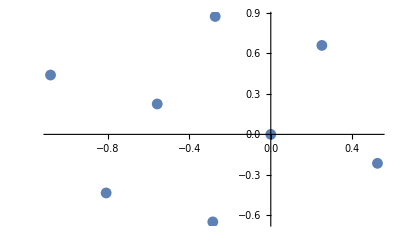

```mathematica
ListPlot[%]
```

{16.0012,15.4688,15.6643,16.2865,15.2761,15.4633,15.7371,16.1684,16.5841,15.7306,16.5344,16.0522,15.4733,14.9573,16.2222,15.4001,15.9069,15.4324,99964,16.3931,16.1034,15.7808,15.5597,16.2018,15.5042,15.4783,15.8299,16.1224,15.9689,15.9171,15.4147,15.5501,15.9346,15.5301,15.6914,15.9841,15.659}
 |  |  |  |

{16.5895,{{62011}}}

{{-0.145472,0.507415,0.849334},{0.234741,-0.816251,0.527856},{0.961111,0.276161,-0.000369565}}

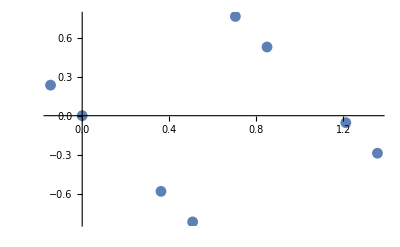

```mathematica
Map[d3ist,Out[162]]
{Max[%],Position[%,Max[%]]}
Out[162][[Last[%][[1,1]]]]
ListPlot[Map[Take[%.#,{1,2}]&,Table[PadLeft[IntegerDigits[i,2],3],{i,0,7}]]]
```

{{-0.201522,0.561803,0.80235},{0.272685,-0.754593,0.596852},{0.940761,0.339068,-0.00112816}}

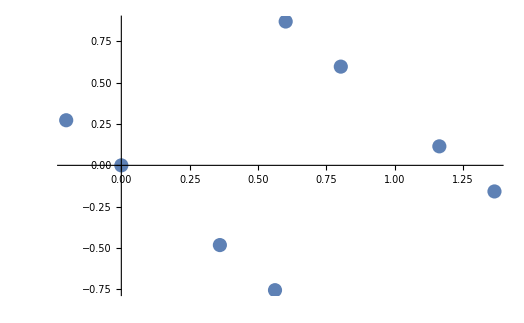

```mathematica
Out[162][[21859]]
ListPlot[Map[Take[%.#,{1,2}]&,Table[PadLeft[IntegerDigits[i,2],3],{i,0,7}]]]
```

```mathematica
Monitor[Table[First[QRDecomposition[RandomReal[{-1,1},{4,4}]]],{k,1,100000}],k];
```

```mathematica
Map[d4ist,Out[180]];
```

```mathematica
Max[Out[182]]
Position[Out[182],%]
```

104.284

{{39218}}

```mathematica
Out[180][[%[[1,1]]]]
```

{{-0.703995,-0.190317,0.640114,0.241711},{0.473946,-0.515924,0.542774,-0.463243},{-0.430763,-0.639459,-0.53131,-0.351063},{0.306936,-0.537302,-0.115585,0.777005}}

```mathematica
Map[Take[%.#,{1,2}]&,Table[PadLeft[IntegerDigits[i,2],4],{i,0,15}]]
```

{{0.,0.},{0.241711,-0.463243},{0.640114,0.542774},{0.881826,0.0795315},{-0.190317,-0.515924},{0.0513943,-0.979167},{0.449797,0.0268501},{0.691509,-0.436393},{-0.703995,0.473946},{-0.462284,0.0107034},{-0.0638808,1.01672},{0.177831,0.553478},{-0.894312,-0.0419781},{-0.652601,-0.505221},{-0.254198,0.500796},{-0.0124864,0.0375535}}

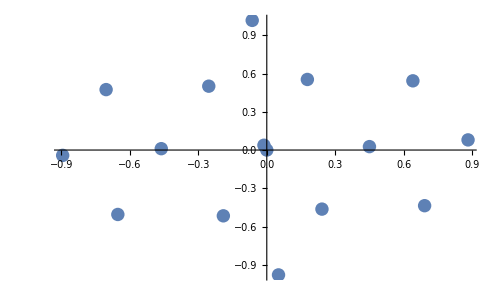

```mathematica
ListPlot[%]
```

```mathematica
ttmat=First[QRDecomposition[RandomReal[{-1,1},{24,24}]]];
```

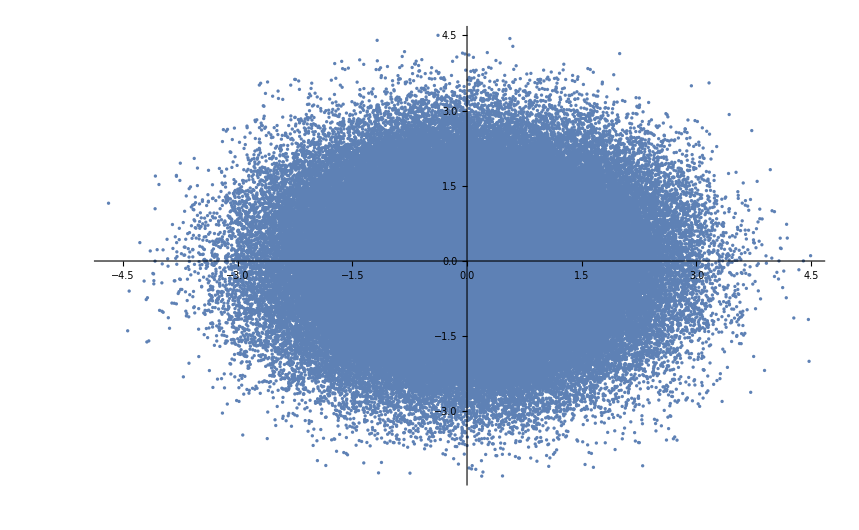

```mathematica
ListPlot[DeleteDuplicates[Join[Map[Take[ttmat.#,{1,2}]&,leech1],Map[Take[ttmat.#,{1,2}]&,leech2],Map[Take[ttmat.#,{1,2}]&,leech3]]]]
```

```mathematica
Length[Flatten[leech2]]/24
```

93104

```mathematica
Join[%,2*Select[golaygreedycode,Total[#]==8&],-2*Select[golaygreedycode,Total[#]==8&]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,2,2,2,2,2,2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-2,2,-2,2,2,2,2,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-2,2,2,-2,2,2,2,2,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-2,2,2,2,-2,2,2,2,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-2,2,2,2,2,-2,2,2,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-2,2,2,2,2,2,-2,2,0,0,0,0,0,0,0},74242,{-2,-2,-2,0,-2,0,0,0,-2,0,0,0,0,0,0,-2,0,0,-2,0,0,-2,0,0},{-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,-2},{-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,-2,-2,-2,-2,0,0,0,0},{-2,-2,-2,-2,0,0,0,0,0,0,0,0,-2,-2,-2,-2,0,0,0,0,0,0,0,0},{-2,-2,-2,-2,0,0,0,0,-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0},{-2,-2,-2,-2,-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
 |  |  |  |

```mathematica
Length[%]
```

74255

```mathematica
Length[{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}]
```

24

```mathematica
leech3=Monitor[Partition[Flatten[Table[Permutations[{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}][[i]]*Map[Piecewise[{{-1, #==1}, {1, #==0}}]&,golaygreedycode[[j]]],{i,1,24},{j,1,4096}]],24],{i,j}]
```

{{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1},{3,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,1,1,1,1,-1,-1,-1,-1},{3,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1},{3,1,1,1,1,1,1,1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1},{3,1,1,1,1,1,1,1,1,1,-1,-1,1,1,-1,-1,-1,-1,1,1,-1,-1,1,1},98293,{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,3},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,-1,-1,-1,-3},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,-1,-1,-1,-1,1,1,1,3},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,3},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-3}}
 |  |  |  |

```mathematica
Length[leech3]
```

98304

```mathematica
leech3[[1]]
```

```mathematica
Select[Table[leech1[[i]].Inverse[√8 LatticeData["Leech"]//Normal],{i,1,Length[leech1]}],Max[Map[Abs,#]]==1&]
```

{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},382,{1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,-1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0}}
 |  |  |  |

```mathematica
Length[Out[72]]
```

396